```mathematica
RadioButtonBar[
Dynamic[fileName],
{
"~/Downloads/optimizerHistory.json",
"/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/optimizerHistory.json"
},Appearance->"Vertical"]

raw=Import[fileName];
```

| ~/Downloads/optimizerHistory.json
 | /Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/optimizerHistory.json

```mathematica
raw= Association[#]&/@raw;
raw=Select[raw,NumericQ[#["maximizeMe"]]&];
```

```mathematica
(*Optional: Drop rows with non-numeric values*)
Length[raw]
raw = Select[raw,AllTrue[Values[#],NumericQ]&];
Length[raw]
```

9974

9963

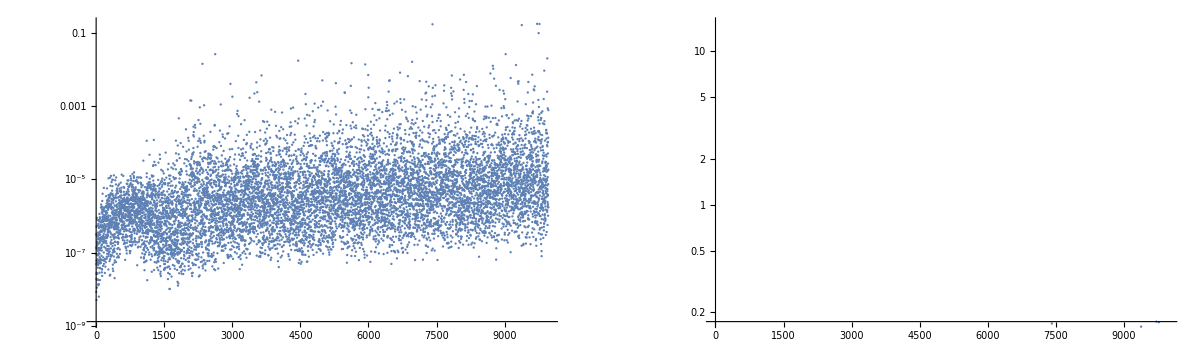

```mathematica
GraphicsGrid[{{
ListLogPlot[
#["maximizeMe"]&/@raw,
(*PlotRange->All,*)
PlotRange->All,
Joined->False,
ImageSize->600
],
ListLogPlot[
#["maximizeMe"]&/@raw,
(*PlotRange->All,*)
PlotRange->{15.,All},
Joined->False,
ImageSize->600
]
}},ImageSize->1200]
```

```mathematica
bestCase = MaximalBy[raw,#["maximizeMe"]&][[1]];
```

```mathematica
(*Format for yml*)
string = ""
Do[
string = string<>key<>" : "<>ToString[bestCase[key],CForm]<>"\n",
{key,Keys[bestCase]}
]
string
```

QA10361kG : -2.9931450424
QA10371kG : 3.424752166
QE10425kG : -5.9377373795
QE10441kG : 5.3041295375
QE10511kG : 4.1091988219
QE10525kG : -4.8040261376
L0BPhaseSet : 3.7915040588
L1PhaseSet : -35.527670309
L2PhaseSet : -37.491254455
L3PhaseSet : -12.0923261819
S1EL_xOffset : 0.00134238
S1EL_yOffset : -0.0002689122
S2EL_xOffset : 0.0007873137
S2EL_yOffset : -0.0001844865
S2ER_xOffset : -0.0009343433
S2ER_yOffset : -0.0015000132
S1ER_xOffset : -0.000121601
S1ER_yOffset : 0.0020602421
XC1FFkG : 0.0052198603
XC3FFkG : -0.0085906824
YC1FFkG : -0.0033407139
YC2FFkG : -0.0476741887
PDrive_mean_x : -5.122e-7
PDrive_mean_y : -4.8277e-6
PDrive_sigma_x : 0.0000396745
PDrive_sigma_y : 0.000027243
PDrive_mean_xp : 0.0001177152
PDrive_mean_yp : -0.0004191598
PDrive_median_x : 3.9153e-6
PDrive_median_y : -2.5694e-6
PDrive_median_xp : 0.0001147023
PDrive_median_yp : -0.0004104556
PDrive_sigmaSI90_x : 0.0000360475
PDrive_sigmaSI90_y : 0.0000201234
PDrive_sigmaSI90_z : 0.0001128456
PDrive_emitSI90_x : 0.000099734
PDrive_emitSI90_y : 0.0000229696
PDrive_zCentroid : 991.3317371518
PWitness_mean_x : -0.0000230549
PWitness_mean_y : -8.1879e-6
PWitness_sigma_x : 0.0001411379
PWitness_sigma_y : 0.0000806327
PWitness_mean_xp : 0.0002169849
PWitness_mean_yp : -0.0004813808
PWitness_median_x : -2.7152e-6
PWitness_median_y : -5.91e-8
PWitness_median_xp : 0.0001715509
PWitness_median_yp : -0.0004695369
PWitness_sigmaSI90_x : 0.0001319353
PWitness_sigmaSI90_y : 0.0000697818
PWitness_sigmaSI90_z : 0.0000108299
PWitness_emitSI90_x : 0.0004236482
PWitness_emitSI90_y : 0.0002419454
PWitness_zCentroid : 991.3319314252
bunchSpacing : 0.0001942733
transverseCentroidOffset : 0.0000227918
lostChargeFraction : 0.0179807579
errorTerm_lostChargeFraction : 0.
errorTerm_bunchSpacing : 0.
errorTerm_transverseOffset : 0.
errorTerm_angleOffset : 0.
errorTerm_mainObjective : 34.3837870825
maximizeMe : 0.1745008479

```mathematica
Norm[{bestCase["PDrive_mean_x"],bestCase["PDrive_mean_y"]}-{bestCase["PWitness_mean_x"],bestCase["PWitness_mean_y"]}]
```

0.0000227918

## Plot all

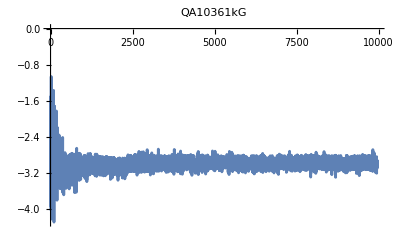
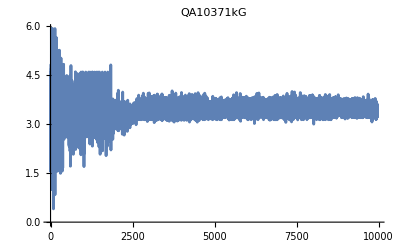
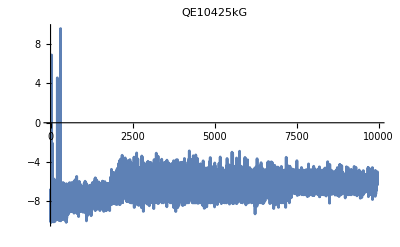
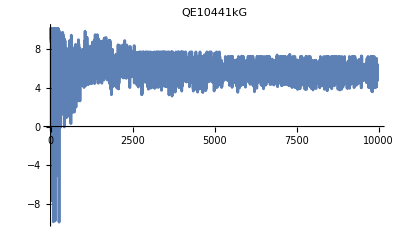
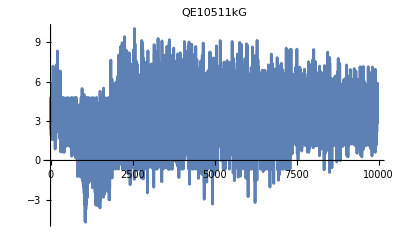
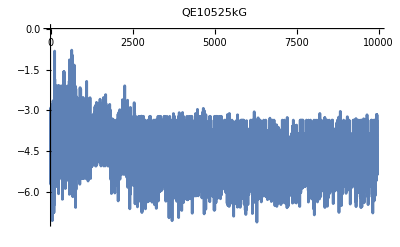
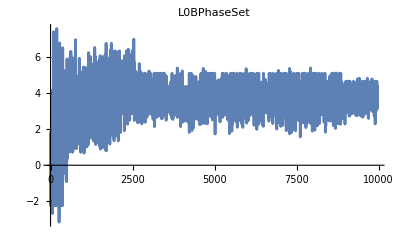
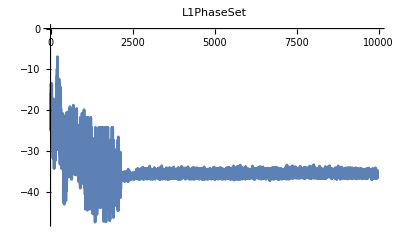
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | 0

```mathematica
imgArr=Table[
ListPlot[
raw[[All,key]],
PlotLabel->key,
ImageSize->400,
LabelStyle->15,
PlotRange->All,
Joined->True
],
{key,Keys[raw[[1]]]}
];

displayCols = 4;
ArrayReshape[
imgArr,{Ceiling[Length[imgArr]/displayCols],displayCols}
]//TableForm
```

## Dump for symbolic regression

Open the CSV in excel, do the automatic suggestion, and resave

```mathematica
Export[
"~/srData.csv",
Dataset[raw]
]
```

~/srData.csv

## Linear model fit

```mathematica
freeVars=Intersection[
Keys[raw[[1]]],
{"L0BPhaseSet","L1PhaseSet","L2PhaseSet","L3PhaseSet","Q1EkG","Q2EkG","Q3EkG","Q4EkG","Q5EkG","Q6EkG","S1ELkG","S2ELkG","S3ELkG","S3ERkG","S2ERkG","S1ERkG","S1EL_xOffset","S1EL_yOffset","S2EL_xOffset","S2EL_yOffset","S2ER_xOffset","S2ER_yOffset","S1ER_xOffset","S1ER_yOffset","Q5FFkG","Q4FFkG","Q3FFkG","Q2FFkG","Q1FFkG","Q0FFkG", "XC1FFkG","XC3FFkG","YC1FFkG","YC2FFkG"}
]
(*Mathematica doesn't like underscores...*)
freeVarsMathematica=StringReplace[#,"_"->""]&/@freeVars;
```

{L0BPhaseSet,L1PhaseSet,L2PhaseSet,L3PhaseSet,S1EL_xOffset,S1EL_yOffset,S1ER_xOffset,S1ER_yOffset,S2EL_xOffset,S2EL_yOffset,S2ER_xOffset,S2ER_yOffset,XC1FFkG,XC3FFkG,YC1FFkG,YC2FFkG}

```mathematica
fitVar = "PDrive_sigmaSI90_z"
fitVar = "bunchSpacing"
```

PDrive_sigmaSI90_z

bunchSpacing

```mathematica
lmData = designMatrix = Table[
row[#]&/@(Append[freeVars,fitVar]),
{row,raw}
];
lm =LinearModelFit[
lmData,
Symbol[#]&/@freeVarsMathematica,
Symbol[#]&/@freeVarsMathematica
]
```

FittedModel[<<1>>]

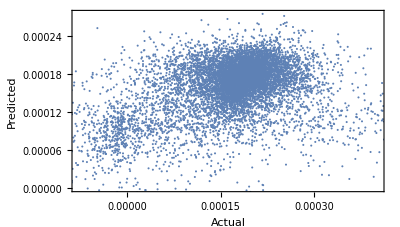

```mathematica
ListPlot[
Transpose[
{
lm["Response"],
lm["PredictedResponse"]
}
],
AspectRatio->Automatic,
Frame->True,
FrameLabel->{"Actual","Predicted"}
]
```

```mathematica
lm["ANOVATable"]
```

| DF | SS | MS | F-Statistic | P-Value
L0BPhaseSet | 1 | 1.94359×10^-6 | 1.94359×10^-6 | 243.999 | 2.33116×10^-54
L1PhaseSet | 1 | 3.6916×10^-6 | 3.6916×10^-6 | 463.444 | 1.64609×10^-100
L2PhaseSet | 1 | 2.03735×10^-6 | 2.03735×10^-6 | 255.77 | 7.31476×10^-57
L3PhaseSet | 1 | 2.57925×10^-6 | 2.57925×10^-6 | 323.8 | 2.88692×10^-71
S1ELxOffset | 1 | 1.25964×10^-7 | 1.25964×10^-7 | 15.8135 | 0.0000703963
S1ELyOffset | 1 | 2.44951×10^-6 | 2.44951×10^-6 | 307.512 | 7.92889×10^-68
S1ERxOffset | 1 | 1.79864×10^-7 | 1.79864×10^-7 | 22.5801 | 2.04382×10^-6
S1ERyOffset | 1 | 3.29389×10^-7 | 3.29389×10^-7 | 41.3516 | 1.33009×10^-10
S2ELxOffset | 1 | 1.84542×10^-7 | 1.84542×10^-7 | 23.1675 | 1.50673×10^-6
S2ELyOffset | 1 | 1.53197×10^-6 | 1.53197×10^-6 | 192.324 | 2.49921×10^-43
S2ERxOffset | 1 | 1.95372×10^-8 | 1.95372×10^-8 | 2.4527 | 0.117355
S2ERyOffset | 1 | 7.03467×10^-8 | 7.03467×10^-8 | 8.83135 | 0.00296808
XC1FFkG | 1 | 2.83974×10^-6 | 2.83974×10^-6 | 356.502 | 3.75039×10^-78
XC3FFkG | 1 | 1.02753×10^-6 | 1.02753×10^-6 | 128.997 | 1.03499×10^-29
YC1FFkG | 1 | 4.20891×10^-8 | 4.20891×10^-8 | 5.28388 | 0.0215444
YC2FFkG | 1 | 1.42931×10^-8 | 1.42931×10^-8 | 1.79436 | 0.180427
Error | 9946 | 0.0000792255 | 7.96557×10^-9 |  | 
Total | 9962 | 0.0000982921 |  |  |

### Fit all dependent vars

```mathematica
allFitVars  = Complement[
Keys[raw[[1]]],
freeVars
];
```

```mathematica
(*
imgArr=Table[
lmData = designMatrix = Table[
row[#]&/@(Append[freeVars,fitVar]),
{row,raw}
];
lm =LinearModelFit[
lmData,
Symbol[#]&/@freeVarsMathematica,
Symbol[#]&/@freeVarsMathematica
];

Show[
ListPlot[
Transpose[
{
lm["Response"],
lm["PredictedResponse"]
}
],
Frame->True,
FrameLabel->{"Actual","Predicted"},
PlotLabel->Row[{fitVar,": ",Style[ToString[lm["RSquared"]],ColorData["Rainbow"][lm["RSquared"]]]}],
ImageSize->400,
AspectRatio->1,
LabelStyle->15,
PlotRange->All
],
Plot[x,{x,Min[lm["Response"]],Max[lm["Response"]]},PlotStyle->Red]
],
{fitVar,allFitVars}
];*)
```

```mathematica
(*displayCols = 4;
ArrayReshape[
imgArr,{Ceiling[Length[imgArr]/displayCols],displayCols}
]//TableForm*)
```

## Parse JSON strings to assoc

```mathematica
(*This is a stupid trick, but ensures numbers in scientific notation are interpreted correctly: https://mathematica.stackexchange.com/questions/15051/reading-in-scientific-notation-from-c-to-mathematica*)
stringToNumber[string_]:=ImportString[string,"Table"][[1,1]]
```

```mathematica
jsonTextToAssoc[string_]:=(
stringParts = StringSplit[StringDelete[#,WhitespaceCharacter],":"]&/@StringSplit[string,"\n"];
Association[#[[1]]->stringToNumber[#[[2]]]&/@stringParts]
)
```

```mathematica
tmp="L0BPhaseSet : -1.7210344516
L1PhaseSet : -20.3120443443
L2PhaseSet : -38.6737055166
L3PhaseSet : -1.4632882388
S1EL_xOffset : 0.0003852549
S1EL_yOffset : -0.0002411137
S2EL_xOffset : -0.0014178669
S2EL_yOffset : 0.0000111705
S2ER_xOffset : -0.002238162
S2ER_yOffset : -0.0006759962
S1ER_xOffset : 0.0010071369
S1ER_yOffset : 0.0003984557
XC1FFkG : 0.2064553639
XC3FFkG : -0.089916372
YC1FFkG : -0.0022311951
YC2FFkG : -0.0085115845";
```

```mathematica
priorSettings = jsonTextToAssoc[tmp]
```

<|L0BPhaseSet→-1.72103,L1PhaseSet→-20.312,L2PhaseSet→-38.6737,L3PhaseSet→-1.46329,S1EL_xOffset→0.000385255,S1EL_yOffset→-0.000241114,S2EL_xOffset→-0.00141787,S2EL_yOffset→0.0000111705,S2ER_xOffset→-0.00223816,S2ER_yOffset→-0.000675996,S1ER_xOffset→0.00100714,S1ER_yOffset→0.000398456,XC1FFkG→0.206455,XC3FFkG→-0.0899164,YC1FFkG→-0.0022312,YC2FFkG→-0.00851158|>

```mathematica
TableForm[
Table[
{
key,priorSettings[key],bestCase[key],bestCase[key]-priorSettings[key]
},
{key,Keys[priorSettings]}
],
TableHeadings->{None,{
Style["Parameter",Bold],
Style["150 μm spacing",Bold],
Style["New spacing",Bold],
Style["Delta",Bold]}}
]
```

Parameter | 150 μm spacing | New spacing | Delta
L0BPhaseSet | -1.72103 | 3.7915 | 5.51254
L1PhaseSet | -20.312 | -35.5277 | -15.2156
L2PhaseSet | -38.6737 | -37.4913 | 1.18245
L3PhaseSet | -1.46329 | -12.0923 | -10.629
S1EL_xOffset | 0.000385255 | 0.00134238 | 0.000957125
S1EL_yOffset | -0.000241114 | -0.000268912 | -0.0000277985
S2EL_xOffset | -0.00141787 | 0.000787314 | 0.00220518
S2EL_yOffset | 0.0000111705 | -0.000184487 | -0.000195657
S2ER_xOffset | -0.00223816 | -0.000934343 | 0.00130382
S2ER_yOffset | -0.000675996 | -0.00150001 | -0.000824017
S1ER_xOffset | 0.00100714 | -0.000121601 | -0.00112874
S1ER_yOffset | 0.000398456 | 0.00206024 | 0.00166179
XC1FFkG | 0.206455 | 0.00521986 | -0.201236
XC3FFkG | -0.0899164 | -0.00859068 | 0.0813257
YC1FFkG | -0.0022312 | -0.00334071 | -0.00110952
YC2FFkG | -0.00851158 | -0.0476742 | -0.0391626